Central difference scheme, accuracy = 2, m≥3

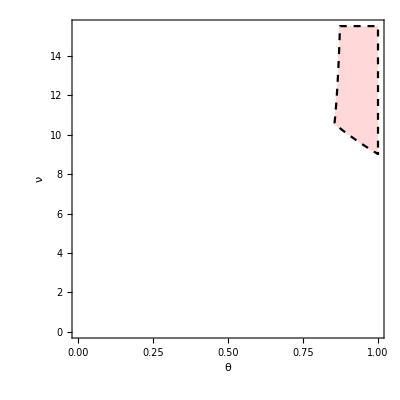

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},BoundaryStyle->{Black,Dashed},FrameLabel->{θ,ν},RotateLabel->False],{m,9,9,2}]
```

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν>0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],ν,Backsubstitution->True],{m,5,5,1}]
```

{(Root[{-2+5 #1-6 #1^2+4 #1^3&,-32-16 #1^2 #2^2+2 #2^3-5 #1 #2^3+6 #1^2 #2^3&},{1,1}]==ν&&Root[-2+5 #1-6 #1^2+4 #1^3&,1]==θ)||(ν≥Root[-8-4 θ^2 #1^2+θ^3 #1^3&,1]&&4/5≤θ&&θ≤1)||(θ<4/5&&Root[-2+5 #1-6 #1^2+4 #1^3&,1]<θ&&ν≤Root[16+(-8 θ+20 θ^2) #1^2+(-4 θ^3+5 θ^4) #1^4&,2]&&Root[-8-4 θ^2 #1^2+θ^3 #1^3&,1]≤ν)}

```mathematica
Root[{-2+5 #1-6 #1^2+4 #1^3&,-32-16 #1^2 #2^2+2 #2^3-5 #1 #2^3+6 #1^2 #2^3&},{1,1}]==ν//RootReduce
```

```mathematica
Root[-16-16 #1-3 #1^2+#1^3&,1]==ν//N
```

6.07011==ν

Central difference scheme, accuracy = 4, stencil width = 5, m≥5

```mathematica
Table[A =DiagonalMatrix[ConstantArray[1/12,m-1],-2,m]+DiagonalMatrix[ConstantArray[-2/3,m-1],-1,m]+DiagonalMatrix[ConstantArray[2/3,m-1],1,m]+DiagonalMatrix[ConstantArray[-1/12,m-1],2,m];
A[[1,m]] = -2/3;A[[1,m-1]] = 1/12;A[[2,m]] = 1/12;A[[m-1,1]] = -1/12;
A[[m,1]] = 2/3;A[[m,2]] = -1/12;(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]],{m,7,7,1}]
```

{{(1+(325 θ^2 ν^2)/144+(1379 θ^4 ν^4)/1152+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)+(2 (1-θ) ν (-(2 θ ν)/3+(θ^2 ν^2)/9-(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736-(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((1-θ) ν (-(θ ν)/12+(4 θ^2 ν^2)/9-(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648-(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-((1-θ) ν ((θ ν)/12+(4 θ^2 ν^2)/9+(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648+(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-(2 (1-θ) ν ((2 θ ν)/3+(θ^2 ν^2)/9+(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736+(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)),(2 (1-θ) ν (1+(325 θ^2 ν^2)/144+(1379 θ^4 ν^4)/1152+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-((1-θ) ν (-(2 θ ν)/3+(θ^2 ν^2)/9-(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736-(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-(2 (1-θ) ν (-(θ ν)/12+(4 θ^2 ν^2)/9-(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648-(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((1-θ) ν (-5/48 θ^2 ν^2+(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912+(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((2 θ ν)/3+(θ^2 ν^2)/9+(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736+(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984),-((1-θ) ν (1+(325 θ^2 ν^2)/144+(1379 θ^4 ν^4)/1152+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((1-θ) ν (-5/48 θ^2 ν^2-(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912-(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(-(θ ν)/12+(4 θ^2 ν^2)/9-(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648-(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)-(2 (1-θ) ν (-5/48 θ^2 ν^2+(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912+(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(2 (1-θ) ν ((2 θ ν)/3+(θ^2 ν^2)/9+(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736+(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)),-(2 (1-θ) ν (-5/48 θ^2 ν^2-(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912-(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(2 (1-θ) ν (-(θ ν)/12+(4 θ^2 ν^2)/9-(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648-(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((1-θ) ν ((θ ν)/12+(4 θ^2 ν^2)/9+(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648+(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(-5/48 θ^2 ν^2+(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912+(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)-((1-θ) ν ((2 θ ν)/3+(θ^2 ν^2)/9+(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736+(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)),((1-θ) ν (-(2 θ ν)/3+(θ^2 ν^2)/9-(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736-(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(-5/48 θ^2 ν^2-(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912-(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)-((1-θ) ν (-(θ ν)/12+(4 θ^2 ν^2)/9-(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648-(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-(2 (1-θ) ν ((θ ν)/12+(4 θ^2 ν^2)/9+(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648+(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(2 (1-θ) ν (-5/48 θ^2 ν^2+(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912+(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)),((1-θ) ν (1+(325 θ^2 ν^2)/144+(1379 θ^4 ν^4)/1152+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))-(2 (1-θ) ν (-(2 θ ν)/3+(θ^2 ν^2)/9-(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736-(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(2 (1-θ) ν (-5/48 θ^2 ν^2-(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912-(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((θ ν)/12+(4 θ^2 ν^2)/9+(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648+(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)-((1-θ) ν (-5/48 θ^2 ν^2+(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912+(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)),-(2 (1-θ) ν (1+(325 θ^2 ν^2)/144+(1379 θ^4 ν^4)/1152+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(-(2 θ ν)/3+(θ^2 ν^2)/9-(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736-(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984)/(1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984)-((1-θ) ν (-5/48 θ^2 ν^2-(85 θ^3 ν^3)/216+(913 θ^4 ν^4)/6912-(67639 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+(2 (1-θ) ν ((θ ν)/12+(4 θ^2 ν^2)/9+(23 θ^3 ν^3)/432+(323 θ^4 ν^4)/648+(16211 θ^5 ν^5)/248832+(312481 θ^6 ν^6)/2985984))/(3 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))+((1-θ) ν ((2 θ ν)/3+(θ^2 ν^2)/9+(2057 θ^3 ν^3)/1728+(3473 θ^4 ν^4)/20736+(57577 θ^5 ν^5)/124416+(312481 θ^6 ν^6)/2985984))/(12 (1+(455 θ^2 ν^2)/144+(9653 θ^4 ν^4)/3456+(2187367 θ^6 ν^6)/2985984))}}

```mathematica
A//Dimensions
```

{7,7}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[1/12,m-1],-2,m]+DiagonalMatrix[ConstantArray[-2/3,m-1],-1,m]+DiagonalMatrix[ConstantArray[2/3,m-1],1,m]+DiagonalMatrix[ConstantArray[-1/12,m-1],2,m];
A[[1,m]] = -2/3;A[[1,m-1]] = 1/12;A[[2,m]] = 1/12;A[[m-1,1]] = -1/12;
A[[m,1]] = 2/3;A[[m,2]] = -1/12;LogicalExpand@Reduce[(0≤θ≤1)&&(ν>0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],ν],{m,5,5,1}]
```

{(Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]==ν&&Root[-8576+13971 #1-5766 #1^2+3844 #1^3&,1]==θ)||(ν≥Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]&&4/5≤θ&&θ≤1)||(θ<4/5&&Root[-8576+13971 #1-5766 #1^2+3844 #1^3&,1]<θ&&ν≤Root[20736+(-18720 θ+46800 θ^2) #1^2+(-20164 θ^3+25205 θ^4) #1^4&,2]&&Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]≤ν)}

```mathematica
{(Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]==ν&&Root[-8576+13971 #1-5766 #1^2+3844 #1^3&,1]==θ)||(ν≥Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]&&4/5≤θ&&θ≤1)||(θ<4/5&&Root[-8576+13971 #1-5766 #1^2+3844 #1^3&,1]<θ&&ν≤Root[20736+(-18720 θ+46800 θ^2) #1^2+(-20164 θ^3+25205 θ^4) #1^4&,2]&&Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]≤ν)}//N
```

{(Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]==ν&&0.726106==θ)||(ν≥Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]&&0.8≤θ&&θ≤1.)||(θ<0.8&&0.726106<θ&&ν≤Root[20736+(-18720 θ+46800 θ^2) #1^2+(-20164 θ^3+25205 θ^4) #1^4&,2]&&Root[-13824+2448 θ #1-14484 θ^2 #1^2+5041 θ^3 #1^3&,1]≤ν)}

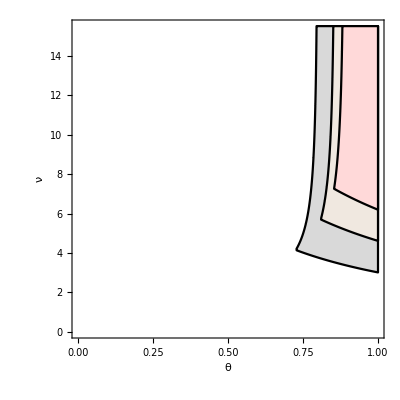

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[1/12,m-1],-2,m]+DiagonalMatrix[ConstantArray[-2/3,m-1],-1,m]+DiagonalMatrix[ConstantArray[2/3,m-1],1,m]+DiagonalMatrix[ConstantArray[-1/12,m-1],2,m];
A[[1,m]] = -2/3;A[[1,m-1]] = 1/12;A[[2,m]] = 1/12;A[[m-1,1]] = -1/12;
A[[m,1]] = 2/3;A[[m,2]] = -1/12;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]}, BoundaryStyle->Black,FrameLabel->{θ,ν},RotateLabel->False],{m,5,9,2}]
```

### Dashed = accuracy 2, cont. = acc. 4, m=5

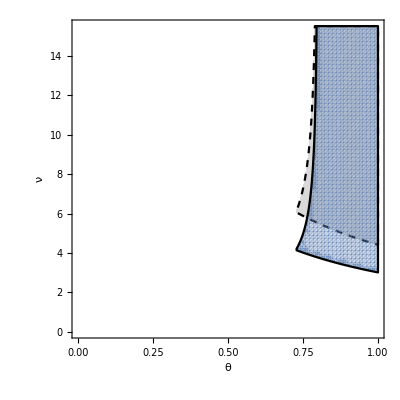

```mathematica
Show[%53,%52]
```

### Dashed = accuracy 2, cont. = acc. 4, m=7

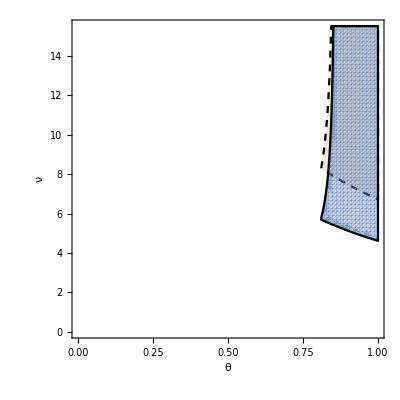

```mathematica
Show[%56,%55]
```

### Dashed = accuracy 2, cont. = acc. 4, m=9

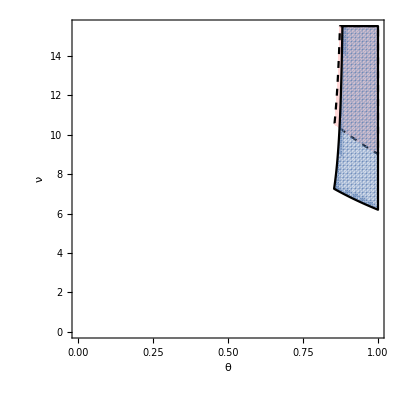

```mathematica
Show[%58,%59]
```

Central difference scheme, accuracy = 6, stencil width = 7, m≥7

```mathematica
m=7;A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;A//MatrixForm
```

(0 | 3/4 | -3/20 | 1/60 | -1/60 | 3/20 | -3/4
-3/4 | 0 | 3/4 | -3/20 | 1/60 | -1/60 | 3/20
3/20 | -3/4 | 0 | 3/4 | -3/20 | 1/60 | -1/60
-1/60 | 3/20 | -3/4 | 0 | 3/4 | -3/20 | 1/60
1/60 | -1/60 | 3/20 | -3/4 | 0 | 3/4 | -3/20
-3/20 | 1/60 | -1/60 | 3/20 | -3/4 | 0 | 3/4
3/4 | -3/20 | 1/60 | -1/60 | 3/20 | -3/4 | 0)

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;LogicalExpand@Reduce[(0≤θ≤1)&&(ν>0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],ν,Backsubstitution->True],{m,8,10,2}]//N
```

{False,False}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;LogicalExpand@Reduce[(0≤θ≤1)&&(ν>0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],ν],{m,11,11,2}]
```

{(Root[-453496320000000000+139072204800000000 θ #1-2108707499520000000 θ^2 #1^2+559838734272000000 θ^3 #1^3-3142691195356800000 θ^4 #1^4+677208894904800000 θ^5 #1^5-1674656791766136000 θ^6 #1^6+310110338251897200 θ^7 #1^7-285256320597856860 θ^8 #1^8+42201834542584201 θ^9 #1^9&,1]==ν&&Root[-1450356766241421963453717179808727831700789595863895724596372907200+10363762454532582913470615717282701950656092391291241737250163575728 #1-56288249011061149378222173655718611034111986577665840755628562300628 #1^2+121298462202409813603617032914731157890534722719605093116312643459656 #1^3-174648494782174475451626691738877913608201433442206865322287514592349 #1^4+172183468921201804583274655880659325235777987142947915659562637020434 #1^5-115591435036848715813675424530240717414973240668499625190896076944156 #1^6+64228678382859591015217890564655941307742585199331024730838475438096 #1^7-18722507663802383921405612248325205063026733096346132465483866395664 #1^8+4160557258622751982534580499627823347339274021410251658996414754592 #1^9&,1]==θ)||(ν≥Root[-453496320000000000+139072204800000000 θ #1-2108707499520000000 θ^2 #1^2+559838734272000000 θ^3 #1^3-3142691195356800000 θ^4 #1^4+677208894904800000 θ^5 #1^5-1674656791766136000 θ^6 #1^6+310110338251897200 θ^7 #1^7-285256320597856860 θ^8 #1^8+42201834542584201 θ^9 #1^9&,1]&&10/11≤θ&&θ≤1)||(θ<10/11&&Root[-1450356766241421963453717179808727831700789595863895724596372907200+10363762454532582913470615717282701950656092391291241737250163575728 #1-56288249011061149378222173655718611034111986577665840755628562300628 #1^2+121298462202409813603617032914731157890534722719605093116312643459656 #1^3-174648494782174475451626691738877913608201433442206865322287514592349 #1^4+172183468921201804583274655880659325235777987142947915659562637020434 #1^5-115591435036848715813675424530240717414973240668499625190896076944156 #1^6+64228678382859591015217890564655941307742585199331024730838475438096 #1^7-18722507663802383921405612248325205063026733096346132465483866395664 #1^8+4160557258622751982534580499627823347339274021410251658996414754592 #1^9&,1]<θ&&ν≤Root[604661760000000000+(-707790182400000000 θ+3892846003200000000 θ^2) #1^2+(-3250952941824000000 θ^3+8940120590016000000 θ^4) #1^4+(-4770401466980160000 θ^5+8745736022796960000 θ^6) #1^6+(-2511262561014662400 θ^7+3452986021395160800 θ^8) #1^8+(-422018345425842010 θ^9+464220179968426211 θ^10) #1^10&,2]&&Root[-453496320000000000+139072204800000000 θ #1-2108707499520000000 θ^2 #1^2+559838734272000000 θ^3 #1^3-3142691195356800000 θ^4 #1^4+677208894904800000 θ^5 #1^5-1674656791766136000 θ^6 #1^6+310110338251897200 θ^7 #1^7-285256320597856860 θ^8 #1^8+42201834542584201 θ^9 #1^9&,1]≤ν)}

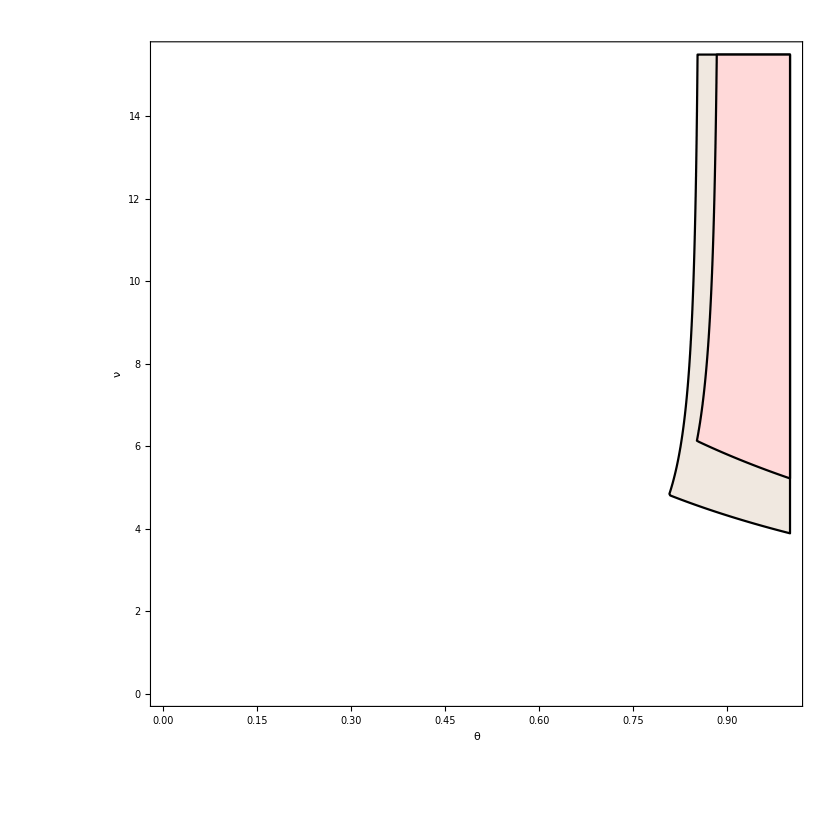

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]}, BoundaryStyle->{Black},FrameLabel->{θ,ν},RotateLabel->False],{m,7,9,2}]
```

### dashed = accuracy 2, black cont. = acc. 4, red = acc. 6, m=7

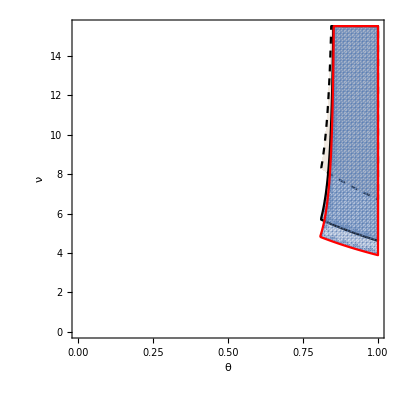

```mathematica
Show[%56,%55,%166]
```

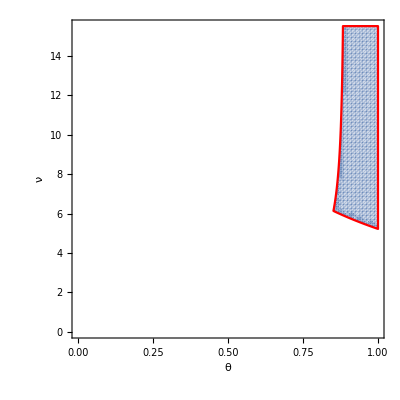

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,(*PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},*) BoundaryStyle->Red,FrameLabel->{θ,ν},RotateLabel->False],{m,9,9,2}]
```

### dashed = accuracy 2, black cont. = acc. 4, red = acc. 6, m=9

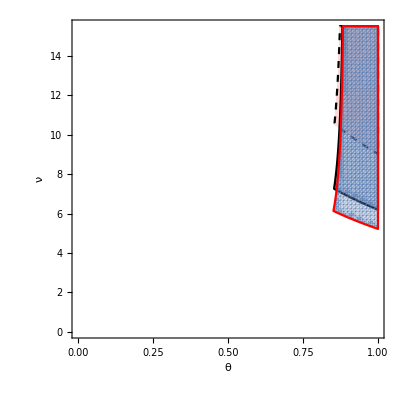

```mathematica
Show[%58,%59,%167]
```

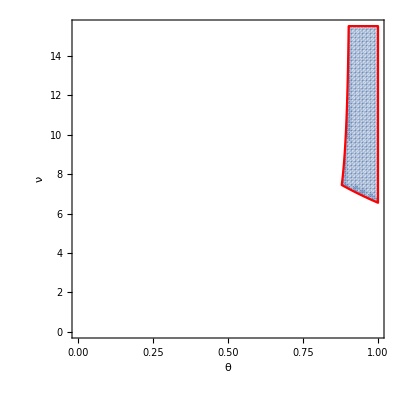

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/60,m-1],-3,m]+DiagonalMatrix[ConstantArray[3/20,m-1],-2,m]+DiagonalMatrix[ConstantArray[-3/4,m-1],-1,m]+DiagonalMatrix[ConstantArray[3/4,m-1],1,m]+DiagonalMatrix[ConstantArray[-3/20,m-1],2,m]+DiagonalMatrix[ConstantArray[1/60,m-1],3,m];
A[[1,m]] = -3/4;A[[1,m-1]] = 3/20;A[[1,m-2]] = -1/60;A[[2,m-1]] = -1/60;A[[3,m]] = -1/60;A[[2,m]] = 3/20;A[[m-2,1]] = 1/60;
A[[m-1,2]] = 1/60;
A[[m,3]] = 1/60;
A[[m-1,1]] = -3/20;
A[[m,1]] = 3/4;A[[m,2]] = -3/20;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,(*PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},*) BoundaryStyle->Red,FrameLabel->{θ,ν},RotateLabel->False],{m,11,11,2}]
```

Spectral collocation, m=4

```mathematica
L=({{0, π/4, 0, -π/4}, {-π/4, 0, π/4, 0}, {0, -π/4, 0, π/4}, {π/4, 0, -π/4, 0}});
```

```mathematica
(Inverse[IdentityMatrix[Length[L]]-θ ν L].(IdentityMatrix[Length[L]]+(1-θ) ν L))[[1]]//Simplify
```

{(8+π^2 θ (-1+2 θ) ν^2)/(8+2 π^2 θ^2 ν^2),(π ν)/(4+π^2 θ^2 ν^2),(π^2 θ ν^2)/(8+2 π^2 θ^2 ν^2),-(π ν)/(4+π^2 θ^2 ν^2)}

### The last entry is negative for ν>0.

Spectral collocation, m=5

```mathematica
L=({{0, π/(5 √(5/8-(√5)/8)), -π/(5 √(5/8+(√5)/8)), π/(5 √(5/8+(√5)/8)), -π/(5 √(5/8-(√5)/8))}, {-π/(5 √(5/8-(√5)/8)), 0, π/(5 √(5/8-(√5)/8)), -π/(5 √(5/8+(√5)/8)), π/(5 √(5/8+(√5)/8))}, {π/(5 √(5/8+(√5)/8)), -π/(5 √(5/8-(√5)/8)), 0, π/(5 √(5/8-(√5)/8)), -π/(5 √(5/8+(√5)/8))}, {-π/(5 √(5/8+(√5)/8)), π/(5 √(5/8+(√5)/8)), -π/(5 √(5/8-(√5)/8)), 0, π/(5 √(5/8-(√5)/8))}, {π/(5 √(5/8-(√5)/8)), -π/(5 √(5/8+(√5)/8)), π/(5 √(5/8+(√5)/8)), -π/(5 √(5/8-(√5)/8)), 0}});
```

```mathematica
((Inverse[IdentityMatrix[Length[L]]-θ ν L].(IdentityMatrix[Length[L]]+(1-θ) ν L))[[1]]//Together)(3125+2500 π^2 θ^2 ν^2+160 π^4 θ^4 ν^4+16 √(5 (5-√5) (5+√5)) π^4 θ^4 ν^4)
```

```mathematica
{1/5 (15625-5000 π^2 θ ν^2+12500 π^2 θ^2 ν^2-640 π^4 θ^3 ν^4-64 √(5 (5-√5) (5+√5)) π^4 θ^3 ν^4+800 π^4 θ^4 ν^4+80 √(5 (5-√5) (5+√5)) π^4 θ^4 ν^4),1/10 (3125 √(2 (5-√5)) π ν+625 √(10 (5-√5)) π ν+2500 π^2 θ ν^2-500 √5 π^2 θ ν^2+1000 √((5-√5) (5+√5)) π^2 θ ν^2+2000 √5 π^2 θ^2 ν^2-1000 √((5-√5) (5+√5)) π^2 θ^2 ν^2+1400 √(2 (5-√5)) π^3 θ^2 ν^3+400 √(10 (5-√5)) π^3 θ^2 ν^3+300 √(2 (5+√5)) π^3 θ^2 ν^3-300 √(10 (5+√5)) π^3 θ^2 ν^3-1000 √(2 (5-√5)) π^3 θ^3 ν^3-200 √(10 (5-√5)) π^3 θ^3 ν^3+400 √(10 (5+√5)) π^3 θ^3 ν^3+320 π^4 θ^3 ν^4+32 √(5 (5-√5) (5+√5)) π^4 θ^3 ν^4),1/10 (-3125 √(2 (5+√5)) π ν+625 √(10 (5+√5)) π ν+2500 π^2 θ ν^2+500 √5 π^2 θ ν^2-1000 √((5-√5) (5+√5)) π^2 θ ν^2-2000 √5 π^2 θ^2 ν^2+1000 √((5-√5) (5+√5)) π^2 θ^2 ν^2+300 √(2 (5-√5)) π^3 θ^2 ν^3+300 √(10 (5-√5)) π^3 θ^2 ν^3-1400 √(2 (5+√5)) π^3 θ^2 ν^3+400 √(10 (5+√5)) π^3 θ^2 ν^3-400 √(10 (5-√5)) π^3 θ^3 ν^3+1000 √(2 (5+√5)) π^3 θ^3 ν^3-200 √(10 (5+√5)) π^3 θ^3 ν^3+320 π^4 θ^3 ν^4+32 √(5 (5-√5) (5+√5)) π^4 θ^3 ν^4),1/10 (3125 √(2 (5+√5)) π ν-625 √(10 (5+√5)) π ν+2500 π^2 θ ν^2+500 √5 π^2 θ ν^2-1000 √((5-√5) (5+√5)) π^2 θ ν^2-2000 √5 π^2 θ^2 ν^2+1000 √((5-√5) (5+√5)) π^2 θ^2 ν^2-300 √(2 (5-√5)) π^3 θ^2 ν^3-300 √(10 (5-√5)) π^3 θ^2 ν^3+1400 √(2 (5+√5)) π^3 θ^2 ν^3-400 √(10 (5+√5)) π^3 θ^2 ν^3+400 √(10 (5-√5)) π^3 θ^3 ν^3-1000 √(2 (5+√5)) π^3 θ^3 ν^3+200 √(10 (5+√5)) π^3 θ^3 ν^3+320 π^4 θ^3 ν^4+32 √(5 (5-√5) (5+√5)) π^4 θ^3 ν^4),1/10 (-3125 √(2 (5-√5)) π ν-625 √(10 (5-√5)) π ν+2500 π^2 θ ν^2-500 √5 π^2 θ ν^2+1000 √((5-√5) (5+√5)) π^2 θ ν^2+2000 √5 π^2 θ^2 ν^2-1000 √((5-√5) (5+√5)) π^2 θ^2 ν^2-1400 √(2 (5-√5)) π^3 θ^2 ν^3-400 √(10 (5-√5)) π^3 θ^2 ν^3-300 √(2 (5+√5)) π^3 θ^2 ν^3+300 √(10 (5+√5)) π^3 θ^2 ν^3+1000 √(2 (5-√5)) π^3 θ^3 ν^3+200 √(10 (5-√5)) π^3 θ^3 ν^3-400 √(10 (5+√5)) π^3 θ^3 ν^3+320 π^4 θ^3 ν^4+32 √(5 (5-√5) (5+√5)) π^4 θ^3 ν^4)}//FullSimplify
```

{3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4,1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν))),1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν))),1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν))),1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))}

```mathematica
And@@({3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4,1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν))),1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν))),1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν))),1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))}≥0//Thread)
```

3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4≥0&&1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))≥0

```mathematica
Reduce[(0≤θ≤1)&&(ν>0)&&3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4≥0]
```

(θ==0&&ν>0)||(0<θ<4/5&&0<ν≤Root[3125+(-1000 π^2 θ+2500 π^2 θ^2) #1^2+(-256 π^4 θ^3+320 π^4 θ^4) #1^4&,2])||(4/5≤θ≤1&&ν>0)

```mathematica
Reduce[(0≤θ≤1)&&(ν>0)&&1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν)))≥0]
```

ν>0&&0≤θ≤1

```mathematica
Reduce[(0≤θ≤1)&&(ν>0)&&1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν)))≥0]
```

0<θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,3]+(250 π θ-150 √5 π θ) #1+40 π^2 θ^2 Root[80-100 #1^2+#1^4&,3] #1^2+64 π^3 θ^3 #1^3&,1]

```mathematica
Reduce[(0≤θ≤1)&&(ν>0)&&1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν)))≥0]
```

0≤θ≤1&&ν>0

```mathematica
Reduce[(0≤θ≤1)&&(ν>0)&&1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))≥0]
```

0<θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1]

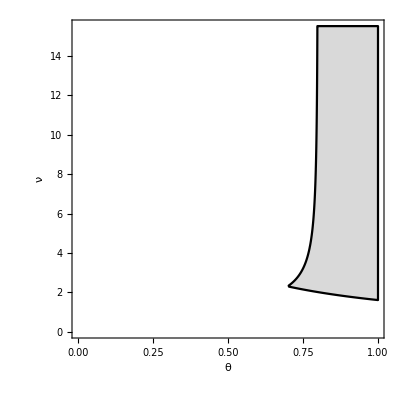

```mathematica
m=5;RegionPlot[Evaluate@(((θ==0&&ν>0)||(0<θ<4/5&&0<ν≤Root[3125+(-1000 π^2 θ+2500 π^2 θ^2) #1^2+(-256 π^4 θ^3+320 π^4 θ^4) #1^4&,2])||(4/5≤θ≤1&&ν>0))&&(0<θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,3]+(250 π θ-150 √5 π θ) #1+40 π^2 θ^2 Root[80-100 #1^2+#1^4&,3] #1^2+64 π^3 θ^3 #1^3&,1])&&(0<θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])),{θ,0,1},{ν,0,15.5},PlotPoints->100,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]}, BoundaryStyle->Black,FrameLabel->{θ,ν},RotateLabel->False]
```

```mathematica
And@@({3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4,1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν))),1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν))),1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν))),1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))}≥0//Thread)
```

3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4≥0&&1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))≥0

```mathematica
Reduce[3125+500 π^2 θ (-2+5 θ) ν^2+64 π^4 θ^3 (-4+5 θ) ν^4≥0&&1/2 π ν (250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (5 √(50+22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (250 √(50-10 √5)+4 π θ ν (125-75 √5+4 π θ ν (-5 √(50-22 √5)+8 π θ ν)))≥0&&1/2 π ν (-250 √(10 (5+√5))+4 π θ ν (25 (5+3 √5)+4 π θ ν (-5 √(50+22 √5)+8 π θ ν)))≥0&&ν>0&&0≤θ≤1]
```

```mathematica
(θ==Root[{-5+#1^2&,80-100 #2^2+#2^4&,2000-100 #3^2+#3^4&,-102400+6560 #3^2+80 #2^2 #3^2-128 #2 #3^3+333600 #4-21600 #1 #4-2800 #2^2 #4-1200 #1 #2^2 #4+7360 #2 #3 #4+1920 #1 #2 #3 #4+160 #2^3 #3 #4-27040 #3^2 #4-336 #1 #3^2 #4-628 #2^2 #3^2 #4+640 #2 #3^3 #4-421600 #4^2+21600 #1 #4^2+16100 #2^2 #4^2+2580 #1 #2^2 #4^2-15840 #2 #3 #4^2-2400 #1 #2 #3 #4^2-600 #2^3 #3 #4^2+35700 #3^2 #4^2-660 #1 #3^2 #4^2+1320 #2^2 #3^2 #4^2-1000 #2 #3^3 #4^2+175600 #4^3-16750 #2^2 #4^3-1350 #1 #2^2 #4^3+10800 #2 #3 #4^3+500 #2^3 #3 #4^3-16750 #3^2 #4^3+1350 #1 #3^2 #4^3-825 #2^2 #3^2 #4^3+500 #2 #3^3 #4^3&},{2,4,4,1}]&&ν==Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])||(Root[{-5+#1^2&,80-100 #2^2+#2^4&,2000-100 #3^2+#3^4&,-102400+6560 #3^2+80 #2^2 #3^2-128 #2 #3^3+333600 #4-21600 #1 #4-2800 #2^2 #4-1200 #1 #2^2 #4+7360 #2 #3 #4+1920 #1 #2 #3 #4+160 #2^3 #3 #4-27040 #3^2 #4-336 #1 #3^2 #4-628 #2^2 #3^2 #4+640 #2 #3^3 #4-421600 #4^2+21600 #1 #4^2+16100 #2^2 #4^2+2580 #1 #2^2 #4^2-15840 #2 #3 #4^2-2400 #1 #2 #3 #4^2-600 #2^3 #3 #4^2+35700 #3^2 #4^2-660 #1 #3^2 #4^2+1320 #2^2 #3^2 #4^2-1000 #2 #3^3 #4^2+175600 #4^3-16750 #2^2 #4^3-1350 #1 #2^2 #4^3+10800 #2 #3 #4^3+500 #2^3 #3 #4^3-16750 #3^2 #4^3+1350 #1 #3^2 #4^3-825 #2^2 #3^2 #4^3+500 #2 #3^3 #4^3&},{2,4,4,1}]<θ<4/5&&Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1]≤ν≤Root[3125+(-1000 π^2 θ+2500 π^2 θ^2) #1^2+(-256 π^4 θ^3+320 π^4 θ^4) #1^4&,2])||(4/5≤θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])//RootReduce
```

(θ==Root[76-602 #1+2123 #1^2-4320 #1^3+5364 #1^4-3888 #1^5+1296 #1^6&,2]&&ν==Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])||(Root[76-602 #1+2123 #1^2-4320 #1^3+5364 #1^4-3888 #1^5+1296 #1^6&,2]<θ<4/5&&Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1]≤ν≤Root[3125+(-1000 π^2 θ+2500 π^2 θ^2) #1^2+(-256 π^4 θ^3+320 π^4 θ^4) #1^4&,2])||(4/5≤θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])

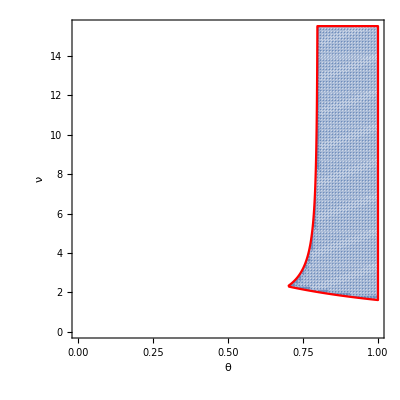

```mathematica
RegionPlot[(θ==Root[76-602 #1+2123 #1^2-4320 #1^3+5364 #1^4-3888 #1^5+1296 #1^6&,2]&&ν==Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1])||(Root[76-602 #1+2123 #1^2-4320 #1^3+5364 #1^4-3888 #1^5+1296 #1^6&,2]<θ<4/5&&Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1]≤ν≤Root[3125+(-1000 π^2 θ+2500 π^2 θ^2) #1^2+(-256 π^4 θ^3+320 π^4 θ^4) #1^4&,2])||(4/5≤θ≤1&&ν≥Root[-125 Root[2000-100 #1^2+#1^4&,4]+(250 π θ+150 √5 π θ) #1-40 π^2 θ^2 Root[80-100 #1^2+#1^4&,4] #1^2+64 π^3 θ^3 #1^3&,1]),{θ,0,1},{ν,0,15.5},PlotPoints->100,(*PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},*) BoundaryStyle->Red,FrameLabel->{θ,ν},RotateLabel->False]
```

Spectral collocation, m=6

```mathematica
L=({{0, π/(2 √3), -π/(6 √3), 0, π/(6 √3), -π/(2 √3)}, {-π/(2 √3), 0, π/(2 √3), -π/(6 √3), 0, π/(6 √3)}, {π/(6 √3), -π/(2 √3), 0, π/(2 √3), -π/(6 √3), 0}, {0, π/(6 √3), -π/(2 √3), 0, π/(2 √3), -π/(6 √3)}, {-π/(6 √3), 0, π/(6 √3), -π/(2 √3), 0, π/(2 √3)}, {π/(2 √3), -π/(6 √3), 0, π/(6 √3), -π/(2 √3), 0}});
```

```mathematica
(Inverse[IdentityMatrix[Length[L]]-θ ν L].(IdentityMatrix[Length[L]]+(1-θ) ν L))[[1,-1]]//Simplify
```

-(3 π ν (9 √3-3 π θ ν+2 √3 π^2 θ^2 ν^2))/(162+90 π^2 θ^2 ν^2+8 π^4 θ^4 ν^4)

```mathematica
Evaluate@LogicalExpand@Reduce[(0≤θ≤1)&&(ν>0)&&-(3 π ν (9 √3-3 π θ ν+2 √3 π^2 θ^2 ν^2))/(162+90 π^2 θ^2 ν^2+8 π^4 θ^4 ν^4)≥0]
```

False

### The last entry is negative for ν>0.

```mathematica
-(3 π ν (9 √3-3 π θ ν+2 √3 π^2 θ^2 ν^2))/(162+90 π^2 θ^2 ν^2+8 π^4 θ^4 ν^4)/.θ->0
```

-(π ν)/(2 √3)

```mathematica
-(3 π ν (9 √3-3 π θ ν+2 √3 π^2 θ^2 ν^2))/(162+90 π^2 θ^2 ν^2+8 π^4 θ^4 ν^4)//Simplify
```

```mathematica
-(9 √3-3 π θ ν+2 √3 π^2 θ^2 ν^2)/.ν->x/(θ π)
```

-9 √3+3 x-2 √3 x^2

```mathematica
Plot[-9 √3+3 x-2 √3 x^2,{x,0,10}]
```

```mathematica
D[-9 √3+3 x-2 √3 x^2,x]==0//Solve
```

{{x→(√3)/4}}

```mathematica
-9 √3+3 x-2 √3 x^2/.x->(√3)/4
```

-(69 √3)/8

Spectral collocation, m=7. To be remarked: the formula R(νL) is computationally very expensive, so the one with the spectral decomposition is easier to use

```mathematica
L=({{0, 1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14], -1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7]}, {-1/7 π Csc[π/7], 0, 1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14], -1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14]}, {1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7], 0, 1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14], -1/7 π Sec[π/14]}, {-1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7], 0, 1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14]}, {1/7 π Sec[π/14], -1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7], 0, 1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14]}, {-1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14], -1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7], 0, 1/7 π Csc[π/7]}, {1/7 π Csc[π/7], -1/7 π Sec[(3 π)/14], 1/7 π Sec[π/14], -1/7 π Sec[π/14], 1/7 π Sec[(3 π)/14], -1/7 π Csc[π/7], 0}});
```

823543+134456 π^2 θ (-2+7 θ) ν^2+38416 π^4 θ^3 (-4+7 θ) ν^4+2304 π^6 θ^5 (-6+7 θ) ν^6≥0&&4 π ν (16807 (2 Cos[π/14]+Cos[(3 π)/14]+3 Sin[π/7])+2 π θ ν (2 π θ ν (343 (20 Cos[π/14]+13 Cos[(3 π)/14]+15 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (3 Cos[π/14]+6 Cos[(3 π)/14]+2 Sin[π/7]))+49 (45 Cos[π/7]+40 Sin[π/14]-13 Sin[(3 π)/14])))+2401 (9 Cos[π/7]+4 Sin[π/14]-Sin[(3 π)/14])))≥0&&4 π ν (16807 (Cos[π/14]-3 Cos[(3 π)/14]-2 Sin[π/7])+2 π θ ν (2 π θ ν (-343 (-13 Cos[π/14]+15 Cos[(3 π)/14]+20 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν-7 (-6 Cos[π/14]+2 Cos[(3 π)/14]+3 Sin[π/7]))+49 (40 Cos[π/7]+13 Sin[π/14]-45 Sin[(3 π)/14])))+2401 (4 Cos[π/7]+Sin[π/14]-9 Sin[(3 π)/14])))≥0&&4 π ν (16807 (3 Cos[π/14]-2 Cos[(3 π)/14]+Sin[π/7])+2 π θ ν (2 π θ ν (343 (15 Cos[π/14]-20 Cos[(3 π)/14]+13 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (2 Cos[π/14]-3 Cos[(3 π)/14]+6 Sin[π/7]))+49 (13 Cos[π/7]+45 Sin[π/14]-40 Sin[(3 π)/14])))+2401 (Cos[π/7]+9 Sin[π/14]-4 Sin[(3 π)/14])))≥0&&4 π ν (-16807 (3 Cos[π/14]-2 Cos[(3 π)/14]+Sin[π/7])+2 π θ ν (2 π θ ν (343 (-15 Cos[π/14]+20 Cos[(3 π)/14]-13 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (-2 Cos[π/14]+3 Cos[(3 π)/14]-6 Sin[π/7]))+49 (13 Cos[π/7]+45 Sin[π/14]-40 Sin[(3 π)/14])))+2401 (Cos[π/7]+9 Sin[π/14]-4 Sin[(3 π)/14])))≥0&&4 π ν (16807 (-Cos[π/14]+3 Cos[(3 π)/14]+2 Sin[π/7])+2 π θ ν (2 π θ ν (343 (-13 Cos[π/14]+15 Cos[(3 π)/14]+20 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (-6 Cos[π/14]+2 Cos[(3 π)/14]+3 Sin[π/7]))+49 (40 Cos[π/7]+13 Sin[π/14]-45 Sin[(3 π)/14])))+2401 (4 Cos[π/7]+Sin[π/14]-9 Sin[(3 π)/14])))≥0&&4 π ν (-16807 (2 Cos[π/14]+Cos[(3 π)/14]+3 Sin[π/7])+2 π θ ν (2 π θ ν (-343 (20 Cos[π/14]+13 Cos[(3 π)/14]+15 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν-7 (3 Cos[π/14]+6 Cos[(3 π)/14]+2 Sin[π/7]))+49 (45 Cos[π/7]+40 Sin[π/14]-13 Sin[(3 π)/14])))+2401 (9 Cos[π/7]+4 Sin[π/14]-Sin[(3 π)/14])))≥0

```mathematica
Reduce[823543+134456 π^2 θ (-2+7 θ) ν^2+38416 π^4 θ^3 (-4+7 θ) ν^4+2304 π^6 θ^5 (-6+7 θ) ν^6≥0&&(0≤θ≤1)&&(ν>0)]
```

(θ==0&&ν>0)||(0<θ<6/7&&0<ν≤Root[823543+(-268912 π^2 θ+941192 π^2 θ^2) #1^2+(-153664 π^4 θ^3+268912 π^4 θ^4) #1^4+(-13824 π^6 θ^5+16128 π^6 θ^6) #1^6&,2])||(6/7≤θ≤1&&ν>0)

```mathematica
Reduce[4 π ν (16807 (2 Cos[π/14]+Cos[(3 π)/14]+3 Sin[π/7])+2 π θ ν (2 π θ ν (343 (20 Cos[π/14]+13 Cos[(3 π)/14]+15 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (3 Cos[π/14]+6 Cos[(3 π)/14]+2 Sin[π/7]))+49 (45 Cos[π/7]+40 Sin[π/14]-13 Sin[(3 π)/14])))+2401 (9 Cos[π/7]+4 Sin[π/14]-Sin[(3 π)/14])))≥0&&(0≤θ≤1)&&(ν>0)]
```

ν>0&&0≤θ≤1

```mathematica
Reduce[4 π ν (16807 (Cos[π/14]-3 Cos[(3 π)/14]-2 Sin[π/7])+2 π θ ν (2 π θ ν (-343 (-13 Cos[π/14]+15 Cos[(3 π)/14]+20 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν-7 (-6 Cos[π/14]+2 Cos[(3 π)/14]+3 Sin[π/7]))+49 (40 Cos[π/7]+13 Sin[π/14]-45 Sin[(3 π)/14])))+2401 (4 Cos[π/7]+Sin[π/14]-9 Sin[(3 π)/14])))≥0&&(0≤θ≤1)&&(ν>0)]
```

$Aborted

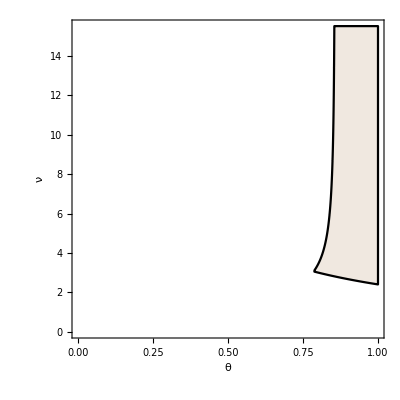

```mathematica
m=7;RegionPlot[823543+134456 π^2 θ (-2+7 θ) ν^2+38416 π^4 θ^3 (-4+7 θ) ν^4+2304 π^6 θ^5 (-6+7 θ) ν^6≥0&&4 π ν (16807 (2 Cos[π/14]+Cos[(3 π)/14]+3 Sin[π/7])+2 π θ ν (2 π θ ν (343 (20 Cos[π/14]+13 Cos[(3 π)/14]+15 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (3 Cos[π/14]+6 Cos[(3 π)/14]+2 Sin[π/7]))+49 (45 Cos[π/7]+40 Sin[π/14]-13 Sin[(3 π)/14])))+2401 (9 Cos[π/7]+4 Sin[π/14]-Sin[(3 π)/14])))≥0&&4 π ν (16807 (Cos[π/14]-3 Cos[(3 π)/14]-2 Sin[π/7])+2 π θ ν (2 π θ ν (-343 (-13 Cos[π/14]+15 Cos[(3 π)/14]+20 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν-7 (-6 Cos[π/14]+2 Cos[(3 π)/14]+3 Sin[π/7]))+49 (40 Cos[π/7]+13 Sin[π/14]-45 Sin[(3 π)/14])))+2401 (4 Cos[π/7]+Sin[π/14]-9 Sin[(3 π)/14])))≥0&&4 π ν (16807 (3 Cos[π/14]-2 Cos[(3 π)/14]+Sin[π/7])+2 π θ ν (2 π θ ν (343 (15 Cos[π/14]-20 Cos[(3 π)/14]+13 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (2 Cos[π/14]-3 Cos[(3 π)/14]+6 Sin[π/7]))+49 (13 Cos[π/7]+45 Sin[π/14]-40 Sin[(3 π)/14])))+2401 (Cos[π/7]+9 Sin[π/14]-4 Sin[(3 π)/14])))≥0&&4 π ν (-16807 (3 Cos[π/14]-2 Cos[(3 π)/14]+Sin[π/7])+2 π θ ν (2 π θ ν (343 (-15 Cos[π/14]+20 Cos[(3 π)/14]-13 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (-2 Cos[π/14]+3 Cos[(3 π)/14]-6 Sin[π/7]))+49 (13 Cos[π/7]+45 Sin[π/14]-40 Sin[(3 π)/14])))+2401 (Cos[π/7]+9 Sin[π/14]-4 Sin[(3 π)/14])))≥0&&4 π ν (16807 (-Cos[π/14]+3 Cos[(3 π)/14]+2 Sin[π/7])+2 π θ ν (2 π θ ν (343 (-13 Cos[π/14]+15 Cos[(3 π)/14]+20 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν+7 (-6 Cos[π/14]+2 Cos[(3 π)/14]+3 Sin[π/7]))+49 (40 Cos[π/7]+13 Sin[π/14]-45 Sin[(3 π)/14])))+2401 (4 Cos[π/7]+Sin[π/14]-9 Sin[(3 π)/14])))≥0&&4 π ν (-16807 (2 Cos[π/14]+Cos[(3 π)/14]+3 Sin[π/7])+2 π θ ν (2 π θ ν (-343 (20 Cos[π/14]+13 Cos[(3 π)/14]+15 Sin[π/7])+2 π θ ν (12 π θ ν (6 π θ ν-7 (3 Cos[π/14]+6 Cos[(3 π)/14]+2 Sin[π/7]))+49 (45 Cos[π/7]+40 Sin[π/14]-13 Sin[(3 π)/14])))+2401 (9 Cos[π/7]+4 Sin[π/14]-Sin[(3 π)/14])))≥0,{θ,0,1},{ν,0,15.5},PlotPoints->100,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]}, BoundaryStyle->Black,FrameLabel->{θ,ν},RotateLabel->False]
```

Spectral collocation, m=8

```mathematica
L=({{0, 1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8], 0, -1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8]}, {-1/8 π Cot[π/8], 0, 1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8], 0, -1/8 π Tan[π/8], π/8}, {π/8, -1/8 π Cot[π/8], 0, 1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8], 0, -1/8 π Tan[π/8]}, {-1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8], 0, 1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8], 0}, {0, -1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8], 0, 1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8]}, {1/8 π Tan[π/8], 0, -1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8], 0, 1/8 π Cot[π/8], -π/8}, {-π/8, 1/8 π Tan[π/8], 0, -1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8], 0, 1/8 π Cot[π/8]}, {1/8 π Cot[π/8], -π/8, 1/8 π Tan[π/8], 0, -1/8 π Tan[π/8], π/8, -1/8 π Cot[π/8], 0}});
```

### The last entry of the 1st row is negative for ν>0.

```mathematica
(Inverse[IdentityMatrix[Length[L]]-θ ν L].(IdentityMatrix[Length[L]]+(1-θ) ν L))[[1,-1]]//Simplify
```

-(π ν (256 (2+√2)-256 π θ ν+32 (7+5 √2) π^2 θ^2 ν^2-64 π^3 θ^3 ν^3+3 (8+3 √2) π^4 θ^4 ν^4))/(2 √2 (1024+896 π^2 θ^2 ν^2+196 π^4 θ^4 ν^4+9 π^6 θ^6 ν^6))

```mathematica
-(π ν (256 (2+√2)-256 π θ ν+32 (7+5 √2) π^2 θ^2 ν^2-64 π^3 θ^3 ν^3+3 (8+3 √2) π^4 θ^4 ν^4))/1
```

```mathematica
(-π ν (256 (2+√2)-256 π θ ν+32 (7+5 √2) π^2 θ^2 ν^2-64 π^3 θ^3 ν^3+3 (8+3 √2) π^4 θ^4 ν^4))/(π ν)
```

```mathematica
-256 (2+√2)+256 π θ ν-32 (7+5 √2) π^2 θ^2 ν^2+64 π^3 θ^3 ν^3-3 (8+3 √2) π^4 θ^4 ν^4/.θ->0
```

-256 (2+√2)

```mathematica
-256 (2+√2)+256 π θ ν-32 (7+5 √2) π^2 θ^2 ν^2+64 π^3 θ^3 ν^3-3 (8+3 √2) π^4 θ^4 ν^4/.ν->y/(π θ)
```

```mathematica
-256 (2+√2)+256 y-32 (7+5 √2) y^2+64 y^3-3 (8+3 √2) y^4//TeXForm
```

-3 \left(8+3 \sqrt{2}\right) y^4+64 y^3-32 \left(7+5 \sqrt{2}\right) y^2+256 y-256 \left(2+\sqrt{2}\right)

```mathematica
Reduce[-256 (2+√2)+256 x-32 (7+5 √2) x^2+64 x^3-3 (8+3 √2) x^4>0]
```

False

Spectral collocation, m=9

```mathematica
L=({{0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9]}, {-1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9]}, {1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3)}, {-(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18]}, {1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18]}, {-1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3)}, {(2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9]}, {-1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0, 1/9 π Csc[π/9]}, {1/9 π Csc[π/9], -1/9 π Csc[(2 π)/9], (2 π)/(9 √3), -1/9 π Sec[π/18], 1/9 π Sec[π/18], -(2 π)/(9 √3), 1/9 π Csc[(2 π)/9], -1/9 π Csc[π/9], 0}});
```

```mathematica
And@@({43046721+7085880 π^2 θ (-2+9 θ) ν^2+3184272 π^4 θ^3 (-4+9 θ) ν^4+1416960 π^6 θ^5 (-2+3 θ) ν^6+16384 π^8 θ^7 (-8+9 θ) ν^8,12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])+1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])+10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])),-10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])-6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])),2 π ν (1594323 √3+354294 π θ ν+866052 √3 π^2 θ^2 ν^2-122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4+55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6+8192 π^7 θ^7 ν^7),-5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])-52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])-12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])),5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])+52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])+12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])),-2 π ν (1594323 √3-354294 π θ ν+866052 √3 π^2 θ^2 ν^2+122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4-55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6-8192 π^7 θ^7 ν^7),10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])+6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])),-12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])-1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])-10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))}≥0//Thread)
```

43046721+7085880 π^2 θ (-2+9 θ) ν^2+3184272 π^4 θ^3 (-4+9 θ) ν^4+1416960 π^6 θ^5 (-2+3 θ) ν^6+16384 π^8 θ^7 (-8+9 θ) ν^8≥0&&12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])+1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])+10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])-6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&2 π ν (1594323 √3+354294 π θ ν+866052 √3 π^2 θ^2 ν^2-122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4+55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6+8192 π^7 θ^7 ν^7)≥0&&-5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])-52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])-12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])+52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])+12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-2 π ν (1594323 √3-354294 π θ ν+866052 √3 π^2 θ^2 ν^2+122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4-55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6-8192 π^7 θ^7 ν^7)≥0&&10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])+6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])-1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])-10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0

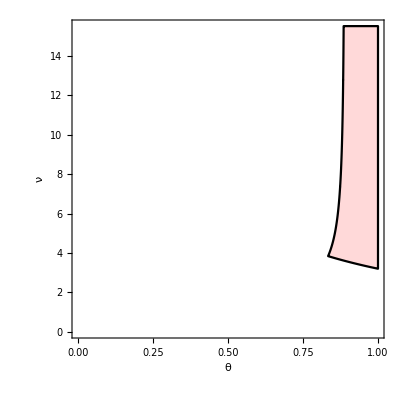

```mathematica
m=9;RegionPlot[43046721+7085880 π^2 θ (-2+9 θ) ν^2+3184272 π^4 θ^3 (-4+9 θ) ν^4+1416960 π^6 θ^5 (-2+3 θ) ν^6+16384 π^8 θ^7 (-8+9 θ) ν^8≥0&&12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])+1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])+10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])-6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&2 π ν (1594323 √3+354294 π θ ν+866052 √3 π^2 θ^2 ν^2-122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4+55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6+8192 π^7 θ^7 ν^7)≥0&&-5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])-52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])-12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])-1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&5184 π^5 θ^4 ν^5 (-126 √3+196 Cos[π/18]+169 √3 Cos[π/9]-413 Sin[π/9])+52488 π^3 θ^2 ν^3 (-63 √3+112 Cos[π/18]+52 √3 Cos[π/9]-110 Sin[π/9])+12288 π^7 θ^6 ν^7 (-2 √3+3 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (-3 √3+8 Cos[π/18]+2 √3 Cos[π/9]-4 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-2 Cos[π/9]-32 Sin[π/18]-4 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189-47 Cos[π/9]-392 Sin[π/18]-169 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-46 Cos[π/9]-448 Sin[π/18]-104 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-2 π ν (1594323 √3-354294 π θ ν+866052 √3 π^2 θ^2 ν^2+122472 π^3 θ^3 ν^3+132192 √3 π^4 θ^4 ν^4-55296 π^5 θ^5 ν^5+27648 √3 π^6 θ^6 ν^6-8192 π^7 θ^7 ν^7)≥0&&10368 π^5 θ^4 ν^5 (63 √3-122 Cos[π/18]+49 √3 Cos[π/9]-218 Sin[π/9])+52488 π^3 θ^2 ν^3 (63 √3-58 Cos[π/18]+56 √3 Cos[π/9]-160 Sin[π/9])+6144 π^7 θ^6 ν^7 (4 √3-24 Cos[π/18]+3 √3 Cos[π/9]-15 Sin[π/9])+1062882 π ν (3 √3-2 Cos[π/18]+4 √3 Cos[π/9]-8 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9-8 Cos[π/9]-2 Sin[π/18]-16 √3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+142 Cos[π/9]-122 Sin[π/18]-196 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189-16 Cos[π/9]-58 Sin[π/18]-224 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0&&-12288 π^7 θ^6 ν^7 (2 √3+6 Cos[π/18]+6 √3 Cos[π/9]-3 Sin[π/9])-1062882 π ν (3 √3+4 Cos[π/18]+√3 Cos[π/9]+7 Sin[π/9])-10368 π^5 θ^4 ν^5 (63 √3+169 Cos[π/18]+61 √3 Cos[π/9]+37 Sin[π/9])-52488 π^3 θ^2 ν^3 (63 √3+104 Cos[π/18]+29 √3 Cos[π/9]+83 Sin[π/9])+4782969 (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9])+16384 π^8 θ^7 ν^8 (1+Cos[π/9]-2 Sin[π/18]-√3 Sin[π/9]+θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+236196 π^2 θ ν^2 (9+31 Cos[π/9]-8 Sin[π/18]-√3 Sin[π/9]+30 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+2304 π^6 θ^5 ν^6 (189+331 Cos[π/9]-338 Sin[π/18]-61 √3 Sin[π/9]+205 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))+11664 π^4 θ^3 ν^4 (189+419 Cos[π/9]-208 Sin[π/18]-29 √3 Sin[π/9]+273 θ (-Cos[π/9]+2 Sin[π/18]+√3 Sin[π/9]))≥0,{θ,0,1},{ν,0,15.5},PlotPoints->100,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]}, BoundaryStyle->Black,FrameLabel->{θ,ν},RotateLabel->False]
```

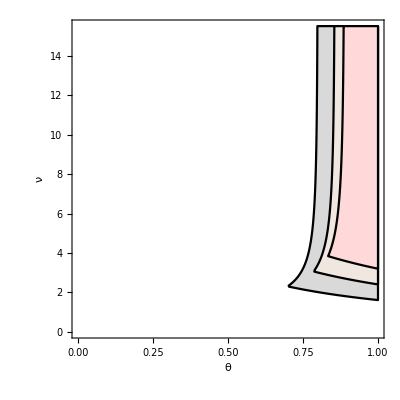

```mathematica
Show[%93,%94,%95]
```

### Observation: for the spectral collocation matrices M with even size, it seems that the last entry of the first row is negative This is true for m=4, 6, 8, 10. Non-trivial polynomial in x (first omitting the positive denominatior, then dividing by π ν, then setting x=θ ν π): first increasing then decreasing, but always negative

### For m=10:

```mathematica
1/10 (1-Cos[j π]+((25+π^2 (-1+θ) θ ν^2) Cos[1/5 (-1+j) π]+5 π ν Sin[1/5 (-1+j) π])/(25+π^2 θ^2 ν^2)+((25+4 π^2 (-1+θ) θ ν^2) Cos[2/5 (-1+j) π]+10 π ν Sin[2/5 (-1+j) π])/(25+4 π^2 θ^2 ν^2)+((25+9 π^2 (-1+θ) θ ν^2) Cos[3/5 (-1+j) π]+15 π ν Sin[3/5 (-1+j) π])/(25+9 π^2 θ^2 ν^2)+((25+16 π^2 (-1+θ) θ ν^2) Cos[4/5 (-1+j) π]+20 π ν Sin[4/5 (-1+j) π])/(25+16 π^2 θ^2 ν^2)+((25+16 π^2 (-1+θ) θ ν^2) Cos[6/5 (-1+j) π]-20 π ν Sin[6/5 (-1+j) π])/(25+16 π^2 θ^2 ν^2)+((25+9 π^2 (-1+θ) θ ν^2) Cos[7/5 (-1+j) π]-15 π ν Sin[7/5 (-1+j) π])/(25+9 π^2 θ^2 ν^2)+((25+4 π^2 (-1+θ) θ ν^2) Cos[8/5 (-1+j) π]-10 π ν Sin[8/5 (-1+j) π])/(25+4 π^2 θ^2 ν^2)+((25+π^2 (-1+θ) θ ν^2) Cos[9/5 (-1+j) π]-5 π ν Sin[9/5 (-1+j) π])/(25+π^2 θ^2 ν^2))/.j->10
```

1/10 ((2 (-5 √(5/8-(√5)/8) π ν+1/4 (1+√5) (25+π^2 (-1+θ) θ ν^2)))/(25+π^2 θ^2 ν^2)+(2 (-10 √(5/8+(√5)/8) π ν+1/4 (-1+√5) (25+4 π^2 (-1+θ) θ ν^2)))/(25+4 π^2 θ^2 ν^2)+(2 (-15 √(5/8+(√5)/8) π ν+1/4 (1-√5) (25+9 π^2 (-1+θ) θ ν^2)))/(25+9 π^2 θ^2 ν^2)+(2 (-20 √(5/8-(√5)/8) π ν+1/4 (-1-√5) (25+16 π^2 (-1+θ) θ ν^2)))/(25+16 π^2 θ^2 ν^2))

```mathematica
-((5 π ν (15625 (√(10-2 √5)+√(2 (5+√5)))-6250 (1+2 √5) π θ ν+625 √2 (17 √(5-√5)+23 √(5+√5)) π^2 θ^2 ν^2-250 (11+28 √5) π^3 θ^3 ν^3+50 √2 (44 √(5-√5)+59 √(5+√5)) π^4 θ^4 ν^4-20 (23+31 √5) π^5 θ^5 ν^5+48 √2 (3 √(5-√5)+2 √(5+√5)) π^6 θ^6 ν^6))/(4 (25+π^2 θ^2 ν^2) (25+4 π^2 θ^2 ν^2) (25+9 π^2 θ^2 ν^2) (25+16 π^2 θ^2 ν^2)))
```

-((5 π ν (15625 (√(10-2 √5)+√(2 (5+√5)))-6250 (1+2 √5) π θ ν+625 √2 (17 √(5-√5)+23 √(5+√5)) π^2 θ^2 ν^2-250 (11+28 √5) π^3 θ^3 ν^3+50 √2 (44 √(5-√5)+59 √(5+√5)) π^4 θ^4 ν^4-20 (23+31 √5) π^5 θ^5 ν^5+48 √2 (3 √(5-√5)+2 √(5+√5)) π^6 θ^6 ν^6))/(4 (25+π^2 θ^2 ν^2) (25+4 π^2 θ^2 ν^2) (25+9 π^2 θ^2 ν^2) (25+16 π^2 θ^2 ν^2)))

```mathematica
%158==%159//Simplify
```

True

```mathematica
1/10 ((2 (-5 √(5/8-(√5)/8) π ν+1/4 (1+√5) (25+π^2 (-1+θ) θ ν^2)))/(25+π^2 θ^2 ν^2)+(2 (-10 √(5/8+(√5)/8) π ν+1/4 (-1+√5) (25+4 π^2 (-1+θ) θ ν^2)))/(25+4 π^2 θ^2 ν^2)+(2 (-15 √(5/8+(√5)/8) π ν+1/4 (1-√5) (25+9 π^2 (-1+θ) θ ν^2)))/(25+9 π^2 θ^2 ν^2)+(2 (-20 √(5/8-(√5)/8) π ν+1/4 (-1-√5) (25+16 π^2 (-1+θ) θ ν^2)))/(25+16 π^2 θ^2 ν^2))//Together
```

```mathematica
-((5 (15625 √(2 (5-√5)) π ν+15625 √(2 (5+√5)) π ν-6250 π^2 θ ν^2-12500 √5 π^2 θ ν^2+10625 √(2 (5-√5)) π^3 θ^2 ν^3+14375 √(2 (5+√5)) π^3 θ^2 ν^3-2750 π^4 θ^3 ν^4-7000 √5 π^4 θ^3 ν^4+2200 √(2 (5-√5)) π^5 θ^4 ν^5+2950 √(2 (5+√5)) π^5 θ^4 ν^5-460 π^6 θ^5 ν^6-620 √5 π^6 θ^5 ν^6+144 √(2 (5-√5)) π^7 θ^6 ν^7+96 √(2 (5+√5)) π^7 θ^6 ν^7))/1)
```

```mathematica
1/(π ν)-5 (15625 √(2 (5-√5)) π ν+15625 √(2 (5+√5)) π ν-6250 π^2 θ ν^2-12500 √5 π^2 θ ν^2+10625 √(2 (5-√5)) π^3 θ^2 ν^3+14375 √(2 (5+√5)) π^3 θ^2 ν^3-2750 π^4 θ^3 ν^4-7000 √5 π^4 θ^3 ν^4+2200 √(2 (5-√5)) π^5 θ^4 ν^5+2950 √(2 (5+√5)) π^5 θ^4 ν^5-460 π^6 θ^5 ν^6-620 √5 π^6 θ^5 ν^6+144 √(2 (5-√5)) π^7 θ^6 ν^7+96 √(2 (5+√5)) π^7 θ^6 ν^7)//Simplify
```

```mathematica
-5 (15625 (√(10-2 √5)+√(2 (5+√5)))-6250 (1+2 √5) π θ ν+625 √2 (17 √(5-√5)+23 √(5+√5)) π^2 θ^2 ν^2-250 (11+28 √5) π^3 θ^3 ν^3+50 √2 (44 √(5-√5)+59 √(5+√5)) π^4 θ^4 ν^4-20 (23+31 √5) π^5 θ^5 ν^5+48 √2 (3 √(5-√5)+2 √(5+√5)) π^6 θ^6 ν^6)/.ν->x/(θ π)//Expand
```

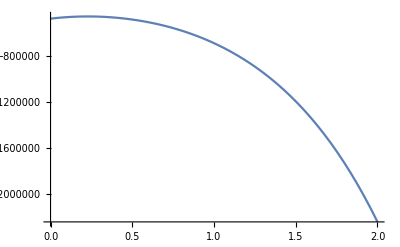

```mathematica
Plot[-78125 √(10-2 √5)-78125 √(2 (5+√5))+31250 x+62500 √5 x-53125 √(2 (5-√5)) x^2-71875 √(2 (5+√5)) x^2+13750 x^3+35000 √5 x^3-11000 √(2 (5-√5)) x^4-14750 √(2 (5+√5)) x^4+2300 x^5+3100 √5 x^5-720 √(2 (5-√5)) x^6-480 √(2 (5+√5)) x^6,{x,0,2}]
```

```mathematica
-5 (15625 (√(10-2 √5)+√(2 (5+√5)))-6250 (1+2 √5) π θ ν+625 √2 (17 √(5-√5)+23 √(5+√5)) π^2 θ^2 ν^2-250 (11+28 √5) π^3 θ^3 ν^3+50 √2 (44 √(5-√5)+59 √(5+√5)) π^4 θ^4 ν^4-20 (23+31 √5) π^5 θ^5 ν^5+48 √2 (3 √(5-√5)+2 √(5+√5)) π^6 θ^6 ν^6)/.θ->0
```

```mathematica
-78125 (√(10-2 √5)+√(2 (5+√5)))//N
```

-480888.